## Plots Z-Prime Decay → neutrinos (Massive), M_Z'=10 TeV, C_ν_Ri^Z'≈ 0.5, m_ν ≈ 100 GeV (Assumed)

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

                          =  (g_PQ^2 M_(Z '))/(12π)√(1-4 m_ν^2/M_Z'^2) ( (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2-2 (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2  )

```mathematica
MassZprime10=10;
MassNu=0.1;
```

```mathematica
gVZp05=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(0.5))
gAZp05=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.499936

-0.0000644793

```mathematica
e^2/(sinsquared(1-sinsquared))
```

0.515835

```mathematica
Zprime10decaymassNu05=MassZprime10/(12π)((gVZp05)^2+(gAZp05)^2+2(MassNu/MassZprime10)^2((gVZp05)^2-2(gAZp05)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
```

66.2975

```mathematica
Zprime10decaymassNu05NF=NumberForm[Zprime10decaymassNu05,16]
```

66.29745417341089

```mathematica
Zprime10decaymassNu05plot=MassZprime10/(12π)((GVZp05)^2+(GAZp05)^2+2(MassNu/MassZprime10)^2((GVZp05)^2-2(GAZp05)^2))√(1-4(MassNu/MassZprime10)^2)*10^3;
```

```mathematica
Plot3D[Zprime10decaymassNu05plot,{GVZp05,0,1},{GAZp05,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ (GeV)"}]
```

-Graphics3D-

## Plots Z-Prime Decay → neutrinos (Massive), M_Z'=8 TeV, C_ν_Ri^Z'≈ 0.5, m_ν ≈ 100 GeV (Assumed)

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

                          =  (g_PQ^2 M_(Z '))/(12π)√(1-4 m_ν^2/M_Z'^2) ( (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2-2 (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2  )

```mathematica
MassZprime8=8;
```

```mathematica
gVZp05=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(0.5))
gAZp05=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.499936

-0.0000644793

```mathematica
Zprime8decaymassNu05=MassZprime8/(12π)((gVZp05)^2+(gAZp05)^2+2(MassNu/MassZprime8)^2((gVZp05)^2-2(gAZp05)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
```

53.038

```mathematica
Zprime8decaymassNu05NF=NumberForm[Zprime8decaymassNu05,16]
```

53.03795875028094

```mathematica
Zprime8decaymassNu05plot=MassZprime8/(12π)((GVZp05)^2+(GAZp05)^2+2(MassNu/MassZprime8)^2((GVZp05)^2-2(GAZp05)^2))√(1-4(MassNu/MassZprime8)^2)*10^3;
```

```mathematica
Plot3D[Zprime8decaymassNu05plot,{GVZp05,0,1},{GAZp05,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ (GeV)"}]
```

-Graphics3D-

## Plots Z-Prime Decay → neutrinos (Massive), M_Z'=5 TeV, C_ν_Ri^Z'≈ 0.5, m_ν ≈ 100 GeV (Assumed)

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

                          =  (g_PQ^2 M_(Z '))/(12π)√(1-4 m_ν^2/M_Z'^2) ( (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2-2 (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2  )

```mathematica
MassZprime5=5;
```

```mathematica
gVZp05=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(0.5))
gAZp05=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.499936

-0.0000644793

```mathematica
Zprime5decaymassNu05=MassZprime5/(12π)((gVZp05)^2+(gAZp05)^2+2(MassNu/MassZprime5)^2((gVZp05)^2-2(gAZp05)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
```

33.1487

```mathematica
Zprime5decaymassNu05NF=NumberForm[Zprime5decaymassNu05,16]
```

33.14869723513552

```mathematica
Zprime5decaymassNu05plot=MassZprime5/(12π)((GVZp05)^2+(GAZp05)^2+2(MassNu/MassZprime5)^2((GVZp05)^2-2(GAZp05)^2))√(1-4(MassNu/MassZprime5)^2)*10^3;
```

```mathematica
Plot3D[Zprime5decaymassNu05plot,{GVZp05,0,1},{GAZp05,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ (GeV)"}]
```

-Graphics3D-

## Compare Change in Z-Prime mass (massless neutrinos)

```mathematica
Zprime10decaymassless05
Zprime8decaymassless05
Zprime5decaymassless05
```

66.2975

53.038

33.1487

```mathematica
Zprime10decaymassless05NF=NumberForm[Zprime10decaymassless05,16]
Zprime8decaymassless05NF=NumberForm[Zprime8decaymassless05,16]
Zprime5decaymassless05NF=NumberForm[Zprime5decaymassless05,16]
```

66.29745815245043

53.03796652196034

33.14872907622521

```mathematica
Zprimedecay05[Mz_]:=Mz/(12π)((gVZp05)^2+(gAZp05)^2)*10^3
```

```mathematica
Zprimedecay05[5]
Zprimedecay05[6]
Zprimedecay05[7]
Zprimedecay05[8]
Zprimedecay05[9]
Zprimedecay05[10]
Zprimedecay05[11]
Zprimedecay05[12]
```

33.1487

39.7785

46.4082

53.038

59.6677

66.2975

72.9272

79.5569

```mathematica
Zprime5decay05NF=NumberForm[Zprimedecay05[5],16]
Zprime6decay05NF=NumberForm[Zprimedecay05[6],16]
Zprime7decay05NF=NumberForm[Zprimedecay05[7],16]
Zprime8decay05NF=NumberForm[Zprimedecay05[8],16]
Zprime9decay05NF=NumberForm[Zprimedecay05[9],16]
Zprime10decay05NF=NumberForm[Zprimedecay05[10],16]
Zprime11decay05NF=NumberForm[Zprimedecay05[11],16]
Zprime12decay05NF=NumberForm[Zprimedecay05[12],16]
```

33.14872907622521

39.77847489147026

46.4082207067153

53.03796652196034

59.66771233720539

66.29745815245043

72.92720396769548

79.55694978294052

```mathematica
DecayTable05=TableForm[{{5,Zprimedecay05[5]},{6,Zprimedecay05[6]},{7,Zprimedecay05[7]},{8,Zprimedecay05[8]},{9,Zprimedecay05[9]},{10,Zprimedecay05[10]},{11,Zprimedecay05[11]},{12,Zprimedecay05[12]}},TableHeadings-> {None,{"TeV","Decay Rate(GeV)"}}]
```

TeV | Decay Rate(GeV)
5 | 33.1487
6 | 39.7785
7 | 46.4082
8 | 53.038
9 | 59.6677
10 | 66.2975
11 | 72.9272
12 | 79.5569

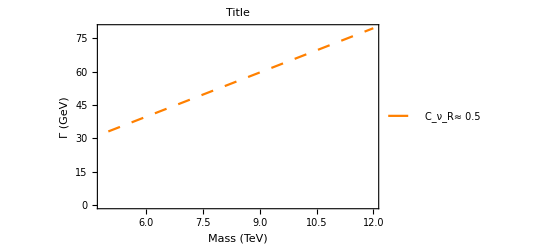

```mathematica
PlotZprimeDecay05=ListPlot[%, Joined-> True,PlotStyle->{Orange,Dashing[Medium]},PlotLegends->{" C_ν_R≈ 0.5"},Frame->True,FrameLabel->{"Mass (TeV)","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
DecayTable05NF=TableForm[{{5,Zprime5decay05NF},{6,Zprime6decay05NF},{7,Zprime7decay05NF},{8,Zprime8decay05NF},{9,Zprime9decay05NF},{10,Zprime10decay05NF},{11,Zprime11decay05NF},{12,Zprime12decay05NF}},TableHeadings-> {None,{"TeV","Decay Rate (Γ → massless)"}}]
```

TeV | Decay Rate (Γ → massless)
5 | 33.14872907622521
6 | 39.77847489147026
7 | 46.4082207067153
8 | 53.03796652196034
9 | 59.66771233720539
10 | 66.29745815245043
11 | 72.92720396769548
12 | 79.55694978294052

## Compare Change in Z-Prime mass (massive neutrinos ≈ 100 GeV)

```mathematica
Zprime10decaymassNu05NF
Zprime8decaymassNu05NF
Zprime5decaymassNu05NF
```

66.29745417341089

53.03795875028094

33.14869723513552

```mathematica
ZprimedecaymassNu05[Mz_]:=Mz/(12π)((gVZp05)^2+(gAZp05)^2+2(MassNu/Mz)^2((gVZp05)^2-2(gAZp05)^2))√(1-4(MassNu/Mz)^2)*10^3;
```

```mathematica
ZprimedecaymassNu05[5]
ZprimedecaymassNu05[6]
ZprimedecaymassNu05[7]
ZprimedecaymassNu05[8]
ZprimedecaymassNu05[9]
ZprimedecaymassNu05[10]
ZprimedecaymassNu05[11]
ZprimedecaymassNu05[12]
```

33.1487

39.7785

46.4082

53.038

59.6677

66.2975

72.9272

79.5569

```mathematica
DecayTablemassNu05=TableForm[{{5,ZprimedecaymassNu05[5]},{6,ZprimedecaymassNu05[6]},{7,ZprimedecaymassNu05[7]},{8,ZprimedecaymassNu05[8]},{9,ZprimedecaymassNu05[9]},{10,ZprimedecaymassNu05[10]},{11,ZprimedecaymassNu05[11]},{12,ZprimedecaymassNu05[12]}},TableHeadings-> {None,{"TeV","Decay Rate (Γ → massive)"}}]
```

TeV | Decay Rate (Γ → massive)
5 | 33.1487
6 | 39.7785
7 | 46.4082
8 | 53.038
9 | 59.6677
10 | 66.2975
11 | 72.9272
12 | 79.5569

```mathematica
Zprime5decaymassNu05NF=NumberForm[ZprimedecaymassNu05[5],16]
Zprime6decaymassNu05NF=NumberForm[ZprimedecaymassNu05[6],16]
Zprime7decaymassNu05NF=NumberForm[ZprimedecaymassNu05[7],16]
Zprime8decaymassNu05NF=NumberForm[ZprimedecaymassNu05[8],16]
Zprime9decaymassNu05NF=NumberForm[ZprimedecaymassNu05[9],16]
Zprime10decaymassNu05NF=NumberForm[ZprimedecaymassNu05[10],16]
Zprime11decaymassNu05NF=NumberForm[ZprimedecaymassNu05[11],16]
Zprime12decaymassNu05NF=NumberForm[ZprimedecaymassNu05[12],16]
```

33.14869723513552

39.77845646758245

46.40820910539025

53.03795875028094

59.66770687899098

66.29745417341089

72.92720097814895

79.55694748018092

```mathematica
DecayTablemassNu05NF=TableForm[{{5,Zprime5decaymassNu05NF},{6,Zprime6decaymassNu05NF},{7,Zprime7decaymassNu05NF},{8,Zprime8decaymassNu05NF},{9,Zprime9decaymassNu05NF},{10,Zprime10decaymassNu05NF},{11,Zprime11decaymassNu05NF},{12,Zprime12decaymassNu05NF}},TableHeadings-> {None,{"TeV","Decay Rate (Γ → massive)"}}]
```

TeV | Decay Rate (Γ → massive)
5 | 33.14869723513552
6 | 39.77845646758245
7 | 46.40820910539025
8 | 53.03795875028094
9 | 59.66770687899098
10 | 66.29745417341089
11 | 72.92720097814895
12 | 79.55694748018092

## Check for any change between massless and massive case

```mathematica
DecayTable05
DecayTablemassNu05
```

TeV | Decay Rate(GeV)
5 | 33.1487
6 | 39.7785
7 | 46.4082
8 | 53.038
9 | 59.6677
10 | 66.2975
11 | 72.9272
12 | 79.5569

TeV | Decay Rate (Γ → massive)
5 | 33.1487
6 | 39.7785
7 | 46.4082
8 | 53.038
9 | 59.6677
10 | 66.2975
11 | 72.9272
12 | 79.5569

## Compare small change in Decay Rate

```mathematica
DecayTable05NF
DecayTablemassNu05NF
```

TeV | Decay Rate (Γ → massless)
5 | 33.14872907622521
6 | 39.77847489147026
7 | 46.4082207067153
8 | 53.03796652196034
9 | 59.66771233720539
10 | 66.29745815245043
11 | 72.92720396769548
12 | 79.55694978294052

TeV | Decay Rate (Γ → massive)
5 | 33.14869723513552
6 | 39.77845646758245
7 | 46.40820910539025
8 | 53.03795875028094
9 | 59.66770687899098
10 | 66.29745417341089
11 | 72.92720097814895
12 | 79.55694748018092

## *Note each end result is multiplied by 10^3to bring Decay Rate units in MeV